Starting PNZSC RIS vs No-RIS Q1 comparison...

Output folder: G:\Thesis\Thesis done 2\Final Folder\PNZSC

NOTE: Rs = 0.5 is stored only for continuity. PNZSC uses Cs > 0, so Rs is not used.

LOCKED: The code uses gammaBar = 10^(rhoMainDB/10) directly for every analytical and MC point.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Parallel kernels launched: 8

Preparing No-RIS local-basis closed-form core...

No-RIS intervals: 331, tail mass: 1.789×10^-28

Preparing RIS closed-form series core...

Precomputing RIS moment coefficients for high-SNR complement branch...

moment coefficients: Ne = 1, power = 0, K = 1

moment coefficients: Ne = 2, power = 1, K = 1800

moment coefficients: Ne = 6, power = 5, K = 1800

moment coefficients: Ne = 15, power = 14, K = 1600

Precomputing RIS high-complement moments...

Precomputing RIS main-series coefficients...

main coefficients: Ne = 1, K = 3600

main coefficients: Ne = 2, K = 3200

main coefficients: Ne = 6, K = 2200

main coefficients: Ne = 15, K = 1800

Computing analytical curves...

Analytical curves finished.

Computing Monte Carlo validation markers...

MC markers finished.

Building professional figure...

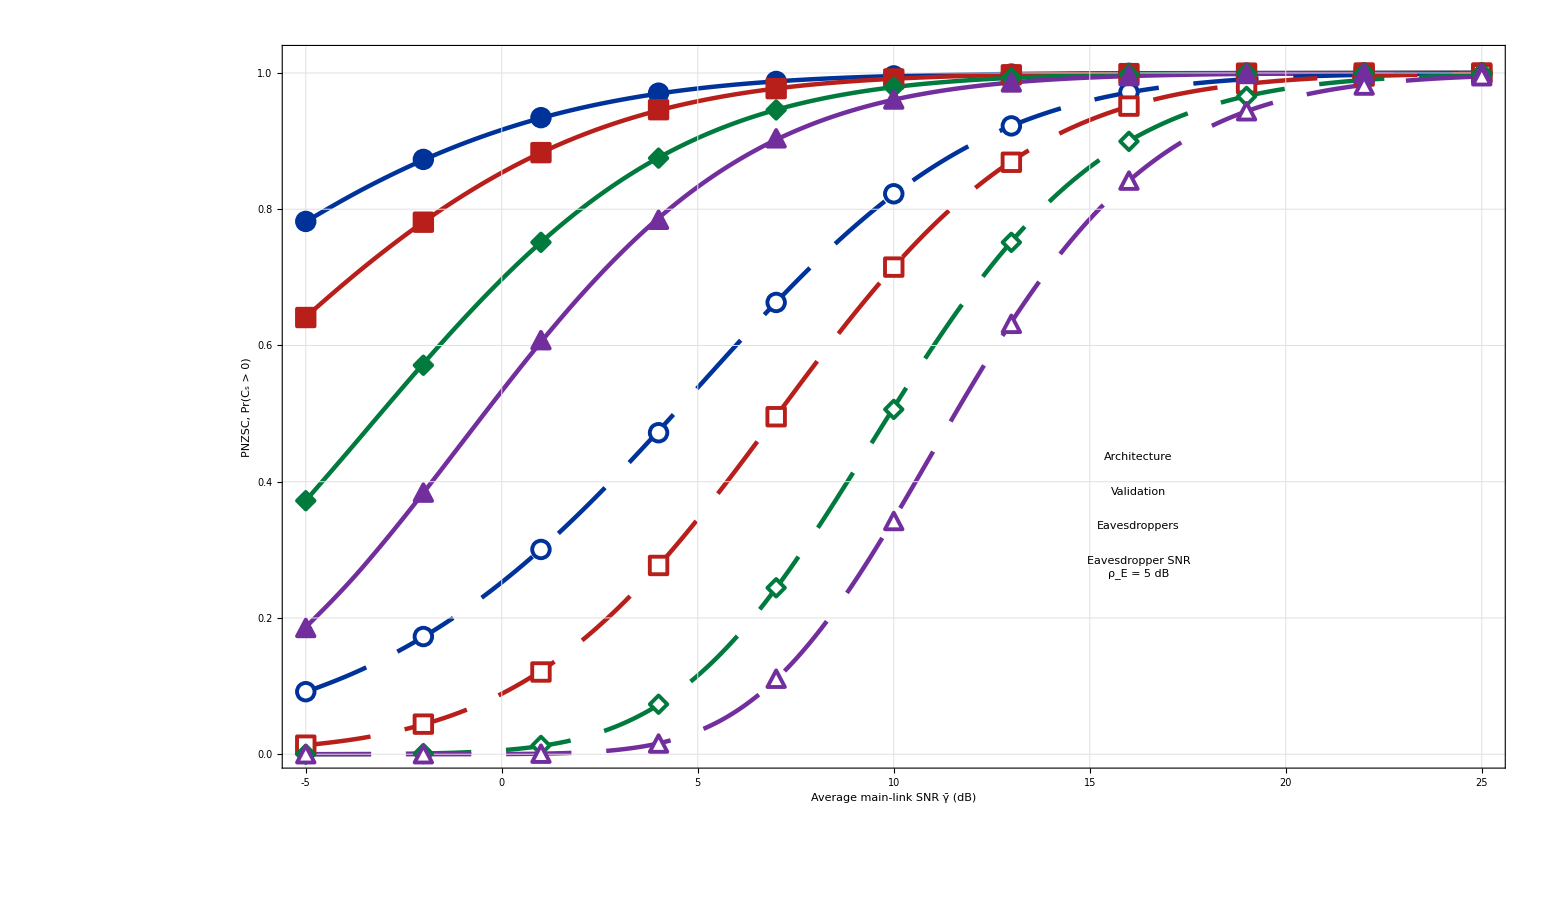

Done. Files saved:

G:\Thesis\Thesis done 2\Final Folder\PNZSC\PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE.pdf

G:\Thesis\Thesis done 2\Final Folder\PNZSC\PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE.png

G:\Thesis\Thesis done 2\Final Folder\PNZSC\PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE.svg

G:\Thesis\Thesis done 2\Final Folder\PNZSC\PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE_RIS_Analytical.csv

G:\Thesis\Thesis done 2\Final Folder\PNZSC\PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE_NoRIS_Analytical.csv

G:\Thesis\Thesis done 2\Final Folder\PNZSC\PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE_RIS_MC.csv

G:\Thesis\Thesis done 2\Final Folder\PNZSC\PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE_NoRIS_MC.csv

Closing subkernels...

```mathematica
(* ::Package::*)(* =========================================================================PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE.wl Purpose:Professional RIS vs No-RIS PNZSC comparison figure for the current single-legitimate-user,multiple-eavesdropper project setting.PNZSC definition:PNZSC=Pr(Cs>0)=Pr(gamma_main>gamma_e,max).Higher PNZSC is better.Unlike SOP,PNZSC normally rises from 0 to 1 as legitimate SNR increases.Analytical Cores:1) No-RIS:ZIS-style local-basis closed-form approximation in the destination Gamma-domain.No NIntegrate and no quadrature kernel.2) RIS:Closed-form Cauchy-series expression with a high-SNR complement evaluation branch for stable top-end behavior.No NIntegrate or NSum.3) Monte Carlo markers are validation only.Locking Note:This script uses only closed-form model parameters.The displayed main-link SNR is converted directly by 10^(rhoMainDB/10) in both RIS and No-RIS.Output:Saves Q1-ready PDF/PNG/SVG and CSV files in the same folder as this.wl file.Run:Open this file in Mathematica and evaluate the whole notebook/script.
=========================================================================*)$HistoryLength=0;
Quiet[CloseKernels[]];
ClearSystemCache[];
Quiet[Remove["Global`*"]];

(* =========================================================================*)
(*1) MASTER PARAMETER PANEL*)
(* =========================================================================*)

(*----------------OUTPUT/RUNTIME----------------*)
codeDir=Module[{d},d=Quiet@Check[DirectoryName[$InputFileName],$Failed];
If[StringQ[d]&&d=!=""&&DirectoryQ[d],d,d=Quiet@Check[NotebookDirectory[],$Failed];
If[StringQ[d]&&d=!=""&&DirectoryQ[d],d,Directory[]]]];
SetDirectory[codeDir];

baseName="PNZSC_RIS_vs_NoRIS_Q1_LOCKED_SINGLE_EXECUTABLE";
outDir=codeDir;                 (*same folder as this.wl file*)
autoOpenFolder=True;
showPlotInNotebook=True;
showRasterPreviewInNotebook=False; (*True=safer if front-end is unstable*)

useParallel=True;
requestedKernels=8;
closeKernelsAtEnd=True;

(*----------------LOCKED PROJECT AXIS/EVE SETTINGS----------------*)
Rs=0.50;                        (*Stored only;PNZSC does not use target Rs*)
rhoEveDB=5;                     (*Fixed Eve average SNR in dB*)
NeList={1,2,6,15};           (*Fixed number of eavesdroppers*)

(*Fixed analytical x-axis points*)
rhoMainDBList=Range[-5,25,1];
(*Fixed MC marker points*)
rhoMainDBMC=Range[-5,25,3];

(*----------------CLOSED-FORM CHANNEL PARAMETERS:NO-RIS---------------- Physical/fading parameters from the No-RIS PNZSC model.*)
alphaM=8/5;                     (*destination generalized-gamma alpha_m>0*)
cM=5/2;                         (*destination shape c_m>0*)
alphaH=3/2;                     (*eavesdropper generalized-gamma alpha_h>0*)
cH=3/2;                         (*eavesdropper shape c_h>0*)

(*----------------CLOSED-FORM CHANNEL PARAMETERS:RIS---------------- RIS physical closed-form parameters mapped from the RIS model.*)
lambdaD=4;                      (*destination RIS square-root Gamma shape lambda_d>0*)
lambdaE=1.3;                    (*eavesdropper RIS square-root Gamma shape lambda_e>0*)
muD=1.8;                        (*destination RIS scale multiplier mu_d>0*)
muE=0.5;                        (*eavesdropper RIS scale multiplier mu_e>0*)

(*----------------NUMERICAL ACCURACY PARAMETERS:NO-RIS---------------- These do not define a new channel.They only control the ZIS local-basis closed-form approximation grid and precision.*)
polyDegNoRIS=3;                  (*safe:2 or 3*)
tTailNoRIS=70.0;                 (*destination Gamma-domain tail cutoff*)
wpNoRIS=70;

(*----------------NUMERICAL ACCURACY PARAMETERS:RIS---------------- These are truncation/branch-evaluation settings only.They are not physical channel parameters and should not be used to tune the model.*)
wpRIS=90;
kMaxRISByN=<|1->3600,2->3200,6->2200,15->1800|>;
highFromDB=<|1->22,2->22,6->16,15->14|>;
kMomentByN=<|1->1,2->1800,6->1800,15->1600|>;
lHigh=28;

(*----------------MONTE CARLO MARKER SETTINGS----------------*)
runMonteCarloMarkers=True;
mcSamplesPerMarker=120000;      (*increase after the first successful run*)
mcChunkSize=10000;
mcSeedBase=20260608;

(*----------------PROFESSIONAL FIGURE SETTINGS----------------*)
plotImageSize=1600;
plotAspectRatio=0.58;
plotYRange={0,1.02};
plotXRange={Min[rhoMainDBList],Max[rhoMainDBList]}; (*full fixed range:-5 to 35 dB*)

fontFamily="Times New Roman";
axisFontSize=18;
tickFontSize=15;
legendFontSize=14;

colors={RGBColor[0.00,0.20,0.60],RGBColor[0.72,0.12,0.10],RGBColor[0.00,0.48,0.24],RGBColor[0.45,0.18,0.62]};

risLineStyle[k_]:=Directive[colors[[k]],AbsoluteThickness[3.2]];
noRISLineStyle[k_]:=Directive[colors[[k]],AbsoluteThickness[3.2],Dashing[{0.030,0.016}]];

mcMarkerDrawSize=18;
mcMarkerEdgeThickness=2.8;
mcLegendMarkerSize=18;
shapeNames={"Circle","Square","Diamond","Triangle"};

markerPrimitive[shape_String]:=Switch[shape,"Circle",Disk[{0,0},0.92],"Square",Rectangle[{-0.85,-0.85},{0.85,0.85}],"Diamond",Polygon[{{0,0.98},{0.98,0},{0,-0.98},{-0.98,0}}],"Triangle",Polygon[{{0,1.02},{-0.95,-0.78},{0.95,-0.78}}],_,Disk[{0,0},0.92]];

filledMarkerGraphic[color_,shape_String]:=Graphics[{EdgeForm[Directive[color,AbsoluteThickness[mcMarkerEdgeThickness]]],FaceForm[color],markerPrimitive[shape]},PlotRange->1.2,ImagePadding->0,Background->None,ImageSize->22];

hollowMarkerGraphic[color_,shape_String]:=Graphics[{EdgeForm[Directive[color,AbsoluteThickness[mcMarkerEdgeThickness]]],FaceForm[White],markerPrimitive[shape]},PlotRange->1.2,ImagePadding->0,Background->None,ImageSize->22];

risPlotMarkers=Table[{filledMarkerGraphic[colors[[k]],shapeNames[[k]]],mcMarkerDrawSize},{k,Length[NeList]}];
noRISPlotMarkers=Table[{hollowMarkerGraphic[colors[[k]],shapeNames[[k]]],mcMarkerDrawSize},{k,Length[NeList]}];

eavesdropperLegendMarkers=Table[{filledMarkerGraphic[colors[[k]],shapeNames[[k]]],mcLegendMarkerSize},{k,Length[NeList]}];

xAxisLabel="Average main-link SNR   \!\(\*OverscriptBox[\(γ\), \(_\)]\)   (dB)";
yAxisLabel="PNZSC,   Pr(\!\(\*SubscriptBox[\(C\), \(s\)]\) > 0)";

(* =========================================================================*)
(*2) INITIALIZATION*)
(* =========================================================================*)

Print["Starting PNZSC RIS vs No-RIS Q1 comparison..."];
Print["Output folder: ",outDir];
Print["NOTE: Rs = ",Rs," is stored only for continuity. PNZSC uses Cs > 0, so Rs is not used."];
Print["LOCKED: The code uses gammaBar = 10^(rhoMainDB/10) directly for every analytical and MC point."];

If[useParallel,Quiet[CloseKernels[]];
LaunchKernels[Min[requestedKernels,$ProcessorCount]];
ParallelEvaluate[$HistoryLength=0;];
Print["Parallel kernels launched: ",$KernelCount];];

dB2lin[x_?NumericQ]:=10.0^(x/10.0);
clip01[x_?NumericQ]:=Min[1.0,Max[0.0,N[x]]];

rhoEbar=dB2lin[rhoEveDB];
nuM=N[alphaM/2.0];
nuH=N[alphaH/2.0];

lowerP[a_?NumericQ,x_?NumericQ]:=Module[{xx=If[x<0,0.0,x]},Quiet[N[GammaRegularized[a,0,xx]],{General::munfl,General::stop}]];

(* =========================================================================*)
(*3) NO-RIS PNZSC:ZIS LOCAL-BASIS CLOSED FORM*)
(* =========================================================================*)

Print["Preparing No-RIS local-basis closed-form core..."];

noRISEveCDFArgFromT[t_?NumericQ,rhoMbar_?NumericQ]:=Module[{gammaM},gammaM=rhoMbar*(t/cM)^(1.0/nuM);
cH*(gammaM/rhoEbar)^nuH];

noRISHofT[t_?NumericQ,rhoMbar_?NumericQ,nE_Integer]:=Module[{arg,Fh},arg=noRISEveCDFArgFromT[t,rhoMbar];
Fh=lowerP[cH,arg];
N[Fh^nE]];

tBreaksNoRIS=DeleteDuplicates@N@Join[Range[0,1,0.025],Range[1.05,5,0.05],Range[5.10,15,0.10],Range[15.25,tTailNoRIS,0.50]];
If[First[tBreaksNoRIS]!=0.0,tBreaksNoRIS=Prepend[tBreaksNoRIS,0.0]];
If[Last[tBreaksNoRIS]<tTailNoRIS,tBreaksNoRIS=Append[tBreaksNoRIS,tTailNoRIS]];
numIntervalsNoRIS=Length[tBreaksNoRIS]-1;

sNodesNoRIS=N@Table[Cos[(2*k+1)*Pi/(2*(polyDegNoRIS+1))],{k,0,polyDegNoRIS}];
vanderSNoRIS=N@Table[sNodesNoRIS[[r]]^j,{r,1,polyDegNoRIS+1},{j,0,polyDegNoRIS}];

noRISLocalTNodes[i_Integer]:=Module[{a=tBreaksNoRIS[[i]],b=tBreaksNoRIS[[i+1]],mid,half},mid=0.5*(a+b);
half=0.5*(b-a);
mid+half*sNodesNoRIS];

noRISRawMomentT[j_Integer,a_?NumericQ,b_?NumericQ]:=N[(Gamma[cM+j]/Gamma[cM])*(GammaRegularized[cM+j,0,b]-GammaRegularized[cM+j,0,a]),40];

noRISScaledMomentT[j_Integer,a_?NumericQ,b_?NumericQ]:=Module[{mid,half,ell},mid=0.5*(a+b);
half=0.5*(b-a);
Sum[Binomial[j,ell] (-mid)^(j-ell) noRISRawMomentT[ell,a,b],{ell,0,j}]/half^j];

nodeTableNoRIS=Table[noRISLocalTNodes[i],{i,1,numIntervalsNoRIS}];
scaledMomentTableNoRIS=Table[Table[noRISScaledMomentT[j,tBreaksNoRIS[[i]],tBreaksNoRIS[[i+1]]],{j,0,polyDegNoRIS}],{i,1,numIntervalsNoRIS}];

tailMassNoRIS=Quiet[N[GammaRegularized[cM,tTailNoRIS]],{General::munfl,General::stop}];
Print["No-RIS intervals: ",numIntervalsNoRIS,", tail mass: ",ScientificForm[tailMassNoRIS,4]];

ClearAll[noRISPNZSCAnalytical];
noRISPNZSCAnalytical[rhoMDB_?NumericQ,nE_Integer]:=Module[{rhoMbar,total=0.0,vals,coeffs,i},rhoMbar=dB2lin[rhoMDB];
For[i=1,i<=numIntervalsNoRIS,i++,vals=noRISHofT[#,rhoMbar,nE]&/@nodeTableNoRIS[[i]];
coeffs=Quiet[LinearSolve[vanderSNoRIS,vals],{LinearSolve::luc,General::stop}];
total+=coeffs.scaledMomentTableNoRIS[[i]];];
clip01[total+tailMassNoRIS]];

(* =========================================================================*)
(*4) RIS PNZSC:CLOSED-FORM SERIES+HIGH COMPLEMENT*)
(* =========================================================================*)

Print["Preparing RIS closed-form series core..."];

betaD[gdB_?NumericQ]:=dB2lin[gdB]*muD;
betaE:=dB2lin[rhoEveDB]*muE;
rhoRoot[gdB_?NumericQ]:=Sqrt[betaD[gdB]/betaE];

kMaxRIS[nE_Integer]:=Lookup[kMaxRISByN,nE,1800];
kMomentRIS[nE_Integer]:=Lookup[kMomentByN,nE,1600];

ClearAll[polyMultiplyTrunc,positivePowerCoeffs];
polyMultiplyTrunc[a_List,b_List,kmax_Integer?NonNegative,wp_Integer]:=Module[{la,lb,maxr,res},la=Length[a];
lb=Length[b];
maxr=Min[kmax,la+lb-2];
res=Table[Sum[a[[i+1]] b[[r-i+1]],{i,Max[0,r-(lb-1)],Min[r,la-1]}],{r,0,maxr}];
res=N[res,wp];
If[Length[res]<kmax+1,Join[res,ConstantArray[SetPrecision[0,wp],kmax+1-Length[res]]],res]];

positivePowerCoeffs[le_?NumericQ,nPow_Integer?NonNegative,kmax_Integer?NonNegative,wp_Integer]:=Module[{q,result,base,power},If[nPow==0,Return[Join[{SetPrecision[1,wp]},ConstantArray[SetPrecision[0,wp],kmax]]]];
q=Table[N[1/Gamma[SetPrecision[le,wp]+r+1],wp],{r,0,kmax}];
result={SetPrecision[1,wp]};
base=q;
power=nPow;
While[power>0,If[OddQ[power],result=polyMultiplyTrunc[result,base,kmax,wp]];
power=Quotient[power,2];
If[power>0,base=polyMultiplyTrunc[base,base,kmax,wp]];];
result];

ClearAll[risSeriesPNZSC];
risSeriesPNZSC[gdB_?NumericQ,nE_Integer?Positive,coeffs_List]:=Module[{rho,kmax,logTerms,maxLog,val,r,ld,le},rho=SetPrecision[rhoRoot[gdB],wpRIS];
ld=SetPrecision[lambdaD,wpRIS];
le=SetPrecision[lambdaE,wpRIS];
kmax=Length[coeffs]-1;
logTerms=Table[Log[SetPrecision[coeffs[[r+1]],wpRIS]]+(nE*le+r) Log[rho]+LogGamma[ld+nE*le+r]-LogGamma[ld]-(ld+nE*le+r) Log[1+nE*rho],{r,0,kmax}];
maxLog=Max[logTerms];
val=Exp[maxLog] Total[Exp[logTerms-maxLog]];
Clip[N[val,20],{0,1}]];

(*High-SNR complement branch:PNZSC=1-E[P(lambdaD,Z_N/rho)].*)
ClearAll[risMomentMaxEveSeries,signedLogSum,risHighComp];

highNs=Keys[highFromDB];

Print["Precomputing RIS moment coefficients for high-SNR complement branch..."];
momentCoeffAssoc=Association@Table[With[{nE=nE,kmax=kMomentRIS[nE]},Print["  moment coefficients: Ne = ",nE,", power = ",nE-1,", K = ",kmax];
nE->positivePowerCoeffs[lambdaE,nE-1,kmax,wpRIS]],{nE,highNs}];

risMomentMaxEveSeries[nE_Integer?Positive,ell_Integer?NonNegative]:=Module[{s,coeffs,kmax,logTerms,maxLog,val,r,le},s=SetPrecision[lambdaD+ell,wpRIS];
le=SetPrecision[lambdaE,wpRIS];
If[nE==1,Return[N[Gamma[le+s]/Gamma[le],wpRIS]]];
coeffs=momentCoeffAssoc[nE];
kmax=Length[coeffs]-1;
logTerms=Table[Log[SetPrecision[coeffs[[r+1]],wpRIS]]+Log[nE]-LogGamma[le]+LogGamma[s+nE*le+r]-(s+nE*le+r) Log[nE],{r,0,kmax}];
maxLog=Max[logTerms];
val=Exp[maxLog] Total[Exp[logTerms-maxLog]];
N[val,wpRIS]];

Print["Precomputing RIS high-complement moments..."];
momentAssoc=Association[Flatten[Table[With[{nE=nE,ell=ell},{nE,ell}->risMomentMaxEveSeries[nE,ell]],{nE,highNs},{ell,0,lHigh}],1]];

signedLogSum[logTerms_List,signs_List]:=Module[{mx,scaled},mx=Max[logTerms];
scaled=Total[signs Exp[logTerms-mx]];
If[scaled==0,Return[0]];
Sign[scaled] Exp[mx+Log[Abs[scaled]]]];

risHighComp[gdB_?NumericQ,nE_Integer?Positive]:=Module[{rho,eta,logTerms,signs,failProb,val,ell,ld},rho=SetPrecision[rhoRoot[gdB],wpRIS];
eta=1/rho;
ld=SetPrecision[lambdaD,wpRIS];
logTerms=Table[(ld+ell) Log[eta]+Log[momentAssoc[{nE,ell}]]-LogGamma[ld]-LogGamma[ell+1]-Log[ld+ell],{ell,0,lHigh}];
signs=Table[(-1)^ell,{ell,0,lHigh}];
failProb=signedLogSum[logTerms,signs];
val=1-failProb;
Clip[N[val,20],{0,1}]];

ClearAll[risPNZSCAnalytical];
risPNZSCAnalytical[gdB_?NumericQ,nE_Integer?Positive,coeffs_List]:=Module[{val,branch},If[KeyExistsQ[highFromDB,nE]&&gdB>=highFromDB[nE],val=risHighComp[gdB,nE];branch=3,val=risSeriesPNZSC[gdB,nE,coeffs];branch=1];
{clip01[val],branch}];

(* =========================================================================*)
(*5) MONTE CARLO MARKERS*)
(* =========================================================================*)

ClearAll[noRISMonteCarloChunked,risMonteCarloChunked];

noRISMonteCarloChunked[rhoMDB_?NumericQ,nE_Integer,samples_Integer,chunk_Integer]:=Module[{rhoMbar,remaining,nNow,good=0,u,gammaM,maxH,z,gammaH,j},rhoMbar=dB2lin[rhoMDB];
remaining=samples;
While[remaining>0,nNow=Min[chunk,remaining];
u=RandomVariate[GammaDistribution[cM,1],nNow];
gammaM=rhoMbar*(u/cM)^(1.0/nuM);
maxH=ConstantArray[0.0,nNow];
For[j=1,j<=nE,j++,z=RandomVariate[GammaDistribution[cH,1],nNow];
gammaH=rhoEbar*(z/cH)^(1.0/nuH);
maxH=MapThread[Max,{maxH,gammaH}];];
good+=Total[Boole[Thread[gammaM>maxH]]];
Clear[u,gammaM,maxH,z,gammaH];
remaining-=nNow;];
N[good/samples]];

risMonteCarloChunked[gdB_?NumericQ,nE_Integer,samples_Integer,chunk_Integer]:=Module[{bd,be,remaining,nNow,good=0,u,gammaD,maxE,v,gammaE,j},bd=betaD[gdB];
be=betaE;
remaining=samples;
While[remaining>0,nNow=Min[chunk,remaining];
u=RandomVariate[GammaDistribution[lambdaD,1],nNow];
gammaD=bd*u^2;
maxE=ConstantArray[0.0,nNow];
For[j=1,j<=nE,j++,v=RandomVariate[GammaDistribution[lambdaE,1],nNow];
gammaE=be*v^2;
maxE=MapThread[Max,{maxE,gammaE}];];
good+=Total[Boole[Thread[gammaD>maxE]]];
Clear[u,gammaD,maxE,v,gammaE];
remaining-=nNow;];
N[good/samples]];

(* =========================================================================*)
(*6) COMPUTE CURVES*)
(* =========================================================================*)

If[useParallel,DistributeDefinitions["Global`"];];

Print["Precomputing RIS main-series coefficients..."];
coeffAssoc=Association@Table[With[{nE=nE,kmax=kMaxRIS[nE]},Print["  main coefficients: Ne = ",nE,", K = ",kmax];
nE->positivePowerCoeffs[lambdaE,nE,kmax,wpRIS]],{nE,NeList}];
If[useParallel,DistributeDefinitions[coeffAssoc]];

Print["Computing analytical curves..."];

noRISAnalyticRows=If[useParallel,Flatten[ParallelTable[{nE,rhoDB,noRISPNZSCAnalytical[rhoDB,nE]},{nE,NeList},{rhoDB,rhoMainDBList},Method->"CoarsestGrained"],1],Flatten[Table[{nE,rhoDB,noRISPNZSCAnalytical[rhoDB,nE]},{nE,NeList},{rhoDB,rhoMainDBList}],1]];

risAnalyticRows=If[useParallel,Flatten[ParallelTable[Module[{tmp=risPNZSCAnalytical[rhoDB,nE,coeffAssoc[nE]]},{nE,rhoDB,tmp[[1]],tmp[[2]]}],{nE,NeList},{rhoDB,rhoMainDBList},Method->"CoarsestGrained"],1],Flatten[Table[Module[{tmp=risPNZSCAnalytical[rhoDB,nE,coeffAssoc[nE]]},{nE,rhoDB,tmp[[1]],tmp[[2]]}],{nE,NeList},{rhoDB,rhoMainDBList}],1]];

noRISCurveData=Association@Table[nE->({#[[2]],#[[3]]}&/@Select[noRISAnalyticRows,#[[1]]==nE&]),{nE,NeList}];

risCurveData=Association@Table[nE->({#[[2]],#[[3]]}&/@Select[risAnalyticRows,#[[1]]==nE&]),{nE,NeList}];

Export[FileNameJoin[{outDir,baseName<>"_NoRIS_Analytical.csv"}],Prepend[noRISAnalyticRows,{"Ne","rhoMain_dB","PNZSC_NoRIS_Analytical"}]];
Export[FileNameJoin[{outDir,baseName<>"_RIS_Analytical.csv"}],Prepend[risAnalyticRows,{"Ne","rhoMain_dB","PNZSC_RIS_Analytical","RIS_Branch_1Series_3High"}]];

Print["Analytical curves finished."];

(* =========================================================================*)
(*7) COMPUTE MC MARKERS*)
(* =========================================================================*)

If[runMonteCarloMarkers,Print["Computing Monte Carlo validation markers..."];
noRISMcRows=If[useParallel,Flatten[ParallelTable[{nE,rhoDB,BlockRandom[SeedRandom[mcSeedBase+100000 nE+1000 Round[rhoDB+100]];
noRISMonteCarloChunked[rhoDB,nE,mcSamplesPerMarker,mcChunkSize]]},{nE,NeList},{rhoDB,rhoMainDBMC},Method->"CoarsestGrained"],1],Flatten[Table[{nE,rhoDB,BlockRandom[SeedRandom[mcSeedBase+100000 nE+1000 Round[rhoDB+100]];
noRISMonteCarloChunked[rhoDB,nE,mcSamplesPerMarker,mcChunkSize]]},{nE,NeList},{rhoDB,rhoMainDBMC}],1]];
risMcRows=If[useParallel,Flatten[ParallelTable[{nE,rhoDB,BlockRandom[SeedRandom[mcSeedBase+500000 nE+1000 Round[rhoDB+100]];
risMonteCarloChunked[rhoDB,nE,mcSamplesPerMarker,mcChunkSize]]},{nE,NeList},{rhoDB,rhoMainDBMC},Method->"CoarsestGrained"],1],Flatten[Table[{nE,rhoDB,BlockRandom[SeedRandom[mcSeedBase+500000 nE+1000 Round[rhoDB+100]];
risMonteCarloChunked[rhoDB,nE,mcSamplesPerMarker,mcChunkSize]]},{nE,NeList},{rhoDB,rhoMainDBMC}],1]];
noRISMcData=Association@Table[nE->({#[[2]],#[[3]]}&/@Select[noRISMcRows,#[[1]]==nE&]),{nE,NeList}];
risMcData=Association@Table[nE->({#[[2]],#[[3]]}&/@Select[risMcRows,#[[1]]==nE&]),{nE,NeList}];
Export[FileNameJoin[{outDir,baseName<>"_NoRIS_MC.csv"}],Prepend[noRISMcRows,{"Ne","rhoMain_dB","PNZSC_NoRIS_MC"}]];
Export[FileNameJoin[{outDir,baseName<>"_RIS_MC.csv"}],Prepend[risMcRows,{"Ne","rhoMain_dB","PNZSC_RIS_MC"}]];
Print["MC markers finished."],noRISMcRows={};
risMcRows={};
noRISMcData=Association@Table[nE->{},{nE,NeList}];
risMcData=Association@Table[nE->{},{nE,NeList}];];

(* =========================================================================*)
(*8) Q1-READY FIGURE*)
(* =========================================================================*)

Print["Building professional figure..."];

allCurveData=Join[Table[risCurveData[nE],{nE,NeList}],Table[noRISCurveData[nE],{nE,NeList}]];

allCurveStyles=Join[Table[risLineStyle[k],{k,Length[NeList]}],Table[noRISLineStyle[k],{k,Length[NeList]}]];

linePlot=ListLinePlot[allCurveData,PlotStyle->allCurveStyles,InterpolationOrder->2,Frame->True,Axes->False,PlotRange->{plotXRange,plotYRange},PlotRangePadding->{{0.010,0.010},{0.010,0.018}},GridLines->{Range[plotXRange[[1]],plotXRange[[2]],5],Range[0,1,0.2]},GridLinesStyle->Directive[GrayLevel[0.88],AbsoluteThickness[0.70]],FrameLabel->{Style[xAxisLabel,axisFontSize,Black,FontFamily->fontFamily],Style[yAxisLabel,axisFontSize,Black,FontFamily->fontFamily]},LabelStyle->Directive[Black,tickFontSize,FontFamily->fontFamily],FrameStyle->Directive[Black,AbsoluteThickness[1.25]],FrameTicksStyle->Directive[Black,tickFontSize,FontFamily->fontFamily],FrameTicks->{{Table[{y,NumberForm[y,{2,1}]},{y,0,1,0.2}],None},{Range[plotXRange[[1]],plotXRange[[2]],5],None}},ImageSize->plotImageSize,AspectRatio->plotAspectRatio,ImagePadding->{{98,18},{82,22}},PlotLegends->None,PlotLabel->None,Background->White];

risMarkerPlot=If[runMonteCarloMarkers,ListPlot[Table[risMcData[nE],{nE,NeList}],PlotStyle->Table[Directive[colors[[k]],AbsoluteThickness[1.4]],{k,Length[NeList]}],PlotMarkers->risPlotMarkers,PlotRange->{plotXRange,plotYRange},PlotRangeClipping->True],Graphics[{}]];

noRISMarkerPlot=If[runMonteCarloMarkers,ListPlot[Table[noRISMcData[nE],{nE,NeList}],PlotStyle->Table[Directive[colors[[k]],AbsoluteThickness[1.4]],{k,Length[NeList]}],PlotMarkers->noRISPlotMarkers,PlotRange->{plotXRange,plotYRange},PlotRangeClipping->True],Graphics[{}]];

corePlot=Show[linePlot,risMarkerPlot,noRISMarkerPlot,PlotRange->{plotXRange,plotYRange},ImageSize->plotImageSize,AspectRatio->plotAspectRatio,Background->White];

styleLegend=LineLegend[{Directive[Black,AbsoluteThickness[3.4]],Directive[Black,AbsoluteThickness[3.4],Dashing[{0.030,0.016}]]},{"RIS analytical","Without-RIS analytical"},LegendMarkerSize->44,LabelStyle->Directive[Black,legendFontSize,FontFamily->fontFamily]];

markerLegend=PointLegend[{Black,Black},{"RIS MC","Without-RIS MC"},LegendMarkers->{{filledMarkerGraphic[Black,"Circle"],mcLegendMarkerSize},{hollowMarkerGraphic[Black,"Circle"],mcLegendMarkerSize}},LabelStyle->Directive[Black,legendFontSize,FontFamily->fontFamily],LegendMarkerSize->mcLegendMarkerSize];

eavesdropperLegend=PointLegend[colors,Table["N\!\(\*SubscriptBox[\(_\), \(e\)]\) = "<>ToString[NeList[[k]]],{k,Length[NeList]}],LegendMarkers->eavesdropperLegendMarkers,LabelStyle->Directive[Black,legendFontSize,FontFamily->fontFamily],LegendMarkerSize->mcLegendMarkerSize];

legendPanel=Framed[Grid[{{Style["Architecture",legendFontSize+1,Bold,FontFamily->fontFamily]},{styleLegend},{Spacer[{1,7}]},{Style["Validation",legendFontSize+1,Bold,FontFamily->fontFamily]},{markerLegend},{Spacer[{1,7}]},{Style["Eavesdroppers",legendFontSize+1,Bold,FontFamily->fontFamily]},{eavesdropperLegend},{Spacer[{1,7}]},{Style["Eavesdropper SNR",legendFontSize+1,Bold,FontFamily->fontFamily]},{Style["\!\(\*SubscriptBox[\(ρ\), \(E\)]\) = 5 dB",legendFontSize,FontFamily->fontFamily]}},Alignment->Left,Spacings->{0,0.35}],FrameStyle->GrayLevel[0.72],Background->Directive[White,Opacity[0.93]],FrameMargins->10,RoundingRadius->4];

(*Positioned inside the figure boundaries to sit comfortably in the empty space between 17 and 25 dB*)
finalPlot=Legended[corePlot,Placed[legendPanel,{0.70,0.35}]];

pdfFile=FileNameJoin[{outDir,baseName<>".pdf"}];
pngFile=FileNameJoin[{outDir,baseName<>".png"}];
svgFile=FileNameJoin[{outDir,baseName<>".svg"}];

Export[pdfFile,finalPlot];
Export[pngFile,finalPlot,ImageResolution->450];
Export[svgFile,finalPlot];

If[showPlotInNotebook,If[showRasterPreviewInNotebook,Print[Rasterize[finalPlot,RasterSize->1400]],Print[finalPlot]]];

Print["Done. Files saved:"];
Print[pdfFile];
Print[pngFile];
Print[svgFile];
Print[FileNameJoin[{outDir,baseName<>"_RIS_Analytical.csv"}]];
Print[FileNameJoin[{outDir,baseName<>"_NoRIS_Analytical.csv"}]];
If[runMonteCarloMarkers,Print[FileNameJoin[{outDir,baseName<>"_RIS_MC.csv"}]];
Print[FileNameJoin[{outDir,baseName<>"_NoRIS_MC.csv"}]];];

If[autoOpenFolder,Quiet[SystemOpen[outDir]]];

If[useParallel&&closeKernelsAtEnd,Print["Closing subkernels..."];
CloseKernels[];];
```